# Zadanie 1

{{-2.23607,-2.},{1.41421,1.},{2.23607,-2.},{-1.41421,1.}}

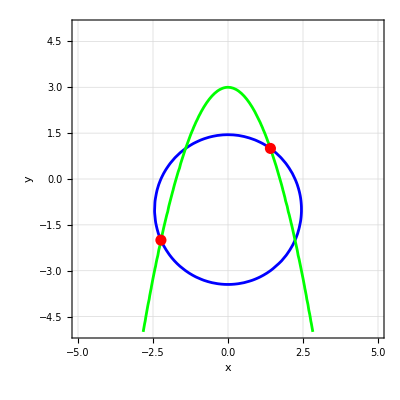

```mathematica
spk = {x,-x^2+3}/. NSolve[{x^2+(y+1)^2==6 && y==-x^2+3},x,y,Reals]
ContourPlot[{x^2+(y+1)^2==6,y==-x^2+3},{x,-5,5},{y,-5,5},ContourStyle->{Blue,Green},Axes->True,AxesLabel->{"x", "y"},GridLines->Automatic,Epilog->{Red,PointSize[0.02],Point[{spk[[1]],spk[[2]]}]}]
```

```mathematica
EuclideanDistance[{0,3},spk[[1]]]
EuclideanDistance[{0,3},spk[[2]]]
```

5.47723

2.44949

# Zadanie 2

```mathematica
g[x_]:= x Exp[-x^2]
solution = N[Exp[-1],3]
```

0.368

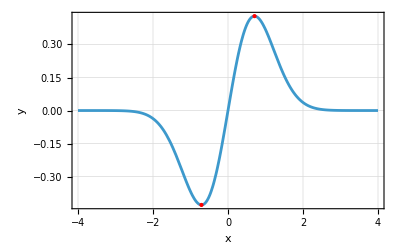

```mathematica
Plot[g[x],{x,-4,4},AxesLabel->{"x", "y"},Frame->True,GridLines->Automatic,Epilog->{Red, Point[{pkt[[1]],pkt[[2]]}] }]
```

```mathematica
Integrate[g[x],{x,0,Infinity}]
pkt = {x,g[x]}/. Solve[D[g[x]==0,x]]
```

1/2

# Zadanie 3

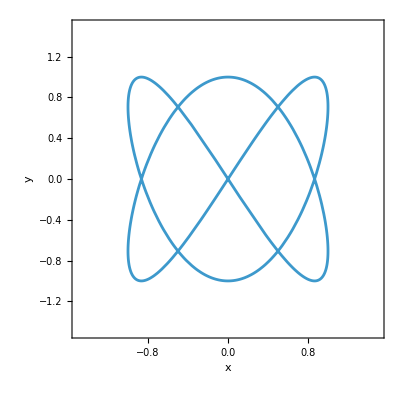

```mathematica
xt[t_]:= Sin[2 t]
yt[t_]:= Sin[3 t]

ParametricPlot[{xt[t],yt[t]},{t,0,2 Pi},PlotRange->{{-1.5,1.5},{-1.5,1.5}},AxesLabel->{"x", "y"},Frame->True]
```

```mathematica
r[t_]:= √((Sin[3 t])^2+( Sin[2 t])^2)
tmax = {t}/. NSolve[D[r[t],t]==0]
rmax = Max[r[tmax]]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{-2.54053},{-1.97288},{-1.5708},{-1.16871},{-0.601061},{0.601061},{1.16871},{1.5708},{1.97288},{2.54053}}

1.34799

```mathematica
N[1/(2 Pi)  Integrate[√((Sin[3 t])^2+( Sin[2 t])^2),{t,0,6}]]
```